选项

Wolfram 语言中的许多函数都有确定其工作方式细节的选项。例如，在创建绘图时，你可以使用 PlotTheme→"Web" 来使用面向网络的视觉主题。在键盘上，如果你输入->(即-后跟>)，则会自动变成→。

一个标准的绘图，没有使用任何选项：

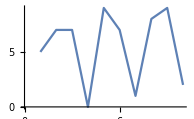

```mathematica
ListLinePlot[RandomInteger[10,10]]
```

PlotTheme 选项设置为 "Web" 的绘图：

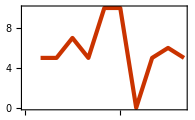

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web"]
```

PlotTheme 选项设置为 "Detailed" 的绘图：

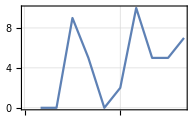

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Detailed"]
```

PlotTheme 选项设置为 "Marketing" 的绘图：

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme-> "Marketing"]
```

-Graphics-

你可以添加更多的选项。例如，Filling 选项指定了要在绘图中添加什么类型的填充。

填充到坐标轴上的绘图：

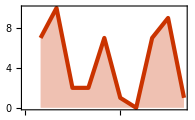

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis]
```

Background 让你可以指定一个背景颜色。

也包括一个背景颜色的选项：

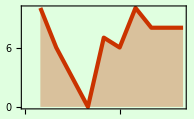

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis,Background->LightGreen]
```

如果您没有指定一个特定的选项，Wolfram 语言将对该选项使用一个预先定义的默认值。大多数情况下，该默认值为 Automatic，这意味着语言将自动确定要做什么。

对于图形来说，PlotRange 选项通常很有用，它可以指定在绘图中包括哪些数值范围。在默认的 PlotRange→Automatic 下，系统会尝试自动显示图表中“有趣”的部分。PlotRange→All 将显示所有的值。

使用默认选项时，除了一个“离群”值之外，其他都会显示出来：

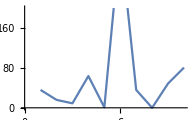

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81}]
```

PlotRange→All 表示包括所有的点：

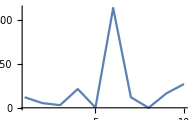

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81},PlotRange->All]
```

PlotRange→30 指定显示30以内的值：

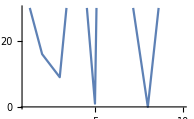

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81},PlotRange->30]
```

PlotRange→{20,100} 指定显示20到100之间的值：

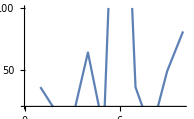

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81},PlotRange->{20,100}]
```

你可以为所有类型的图形指定范围。在 GeoListPlot 和 GeoGraphics 中，你可以使用选项 GeoRange 来指定将世界的哪一部分包括在图中。

在默认情况下，法国的地理图几乎只包括法国：

```mathematica
GeoListPlot[LinguisticAssistant]
```

-Graphics-

要求包括整个欧洲的范围：

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->LinguisticAssistant]
```

-Graphics-

GeoRange→All 将指定使用整个世界：

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->All]
```

-Graphics-

GeoListPlot 还有许多其他选项。例如，GeoBackground 指定了应该使用哪种背景。GeoLabels 用于添加标签。Joined 用于将各点连接起来。

使用浮雕地图作为背景：

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->LinguisticAssistant,GeoBackground->"ReliefMap"]
```

-Graphics-

自动添加地理对象的标签：

```mathematica
GeoListPlot[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},GeoLabels->Automatic]
```

-Graphics-

需要将这些点连接起来：

```mathematica
GeoListPlot[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},Joined->True]
```

-Graphics-

ListLinePlot 函数有 57 个不同的选项可以设置；GeoListPlot 有54个。有些选项是所有图形函数所共有的。例如，AspectRatio 决定了图形的整体形状，它指定了高度和宽度的比例。

纵横比为1/3，则绘图的宽度是其高度的3倍：

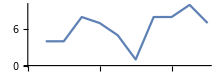

```mathematica
ListLinePlot[RandomInteger[10,10],AspectRatio->1/3]
```

ImageSize 选项指定了图形的整体大小。

绘制一个整体图像大小为“微小”的圆：

```mathematica
Graphics[Circle[ ],ImageSize->Tiny]
```

-Graphics-

使用从 5 到 50 像素之间的指定图像尺寸绘制圆圈：

```mathematica
Table[Graphics[Circle[ ],ImageSize->n],{n,5,50,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

不仅仅 Graphics 允许设置选项，很多其他函数也是如此。一个例子是 Style，它支持许多选项。

设置选项以使用“Chalkboard”字体来样式化文本：

```mathematica
Style["text in a different font",20,FontFamily-> "Chalkboard"]
```

text in a different font

使用选项来描述输出的细节是很常见的，例如在 WordCloud 中。

用随机的单词方向来创建一个词云：

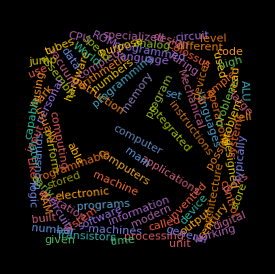

```mathematica
WordCloud[DeleteStopwords[WikipediaData["computer"]],WordOrientation->"Random"]
```

Grid 有许多选项。Frame 选项用于控制是否以及如何绘制边框。

创建一个乘法表，每个条目周围都有一个边框：

```mathematica
Grid[Table[i*j,{i,5},{j,5}],Frame->All]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

与 Graphics 一样，Grid 也可以使用 Background 选项：

```mathematica
Grid[Table[i*j,{i,5},{j,5}],Frame->All,Background->LightYellow]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

词汇

PlotTheme |   | 绘图的主题(比如 "Web"、"Detailed" 等等)
Filling |   | 向绘图中添加填充(Axis、Bottom 等等)
PlotRange |   | 绘图中包含的数值范围(All 等)
GeoRange |   | 要包含的地理范围(All、特定国家等等)
GeoBackground |   | 背景地图("ReliefMap"、"OutlineMap" 等等)
 GeoLabels |   | 向地图中添加标签(比如 Automatic)
Joined |   | 是否要将点进行连接(True、False)
Background |   | 背景颜色
AspectRatio |   | 宽高比
ImageSize |   | 图像大小，单位为像素
Frame |   | 是否包含边框(True、All 等等)
FontFamily |   | 要使用的字体系列(比如 "Helvetica")
WordOrientation |   | 在词云中以什么方向摆放单词

"共有 13 道习题"
"以及 8 道附加题" | "开始练习 »"

为 Range[10] 绘制一个网络主题的点集图。»

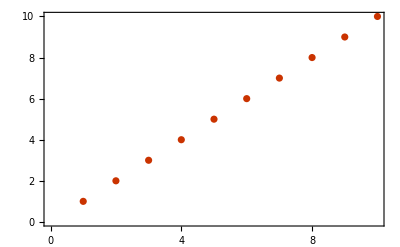
| 期望输出： |  
  | -Graphics- |

为 Range[10] 创建一个点集图，并填充到轴。»

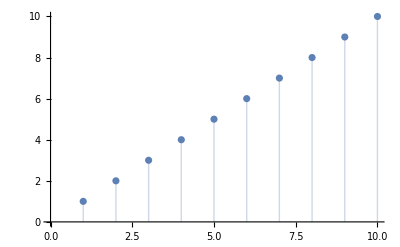
| 期望输出： |  
  | -Graphics- |

为 Range[10] 创建一个点集图，使用黄色背景。»

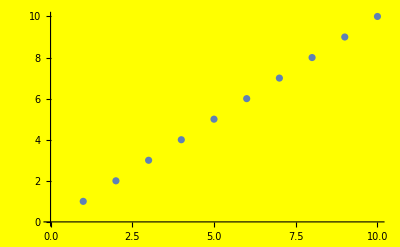
| 期望输出： |  
  | -Graphics- |

绘制一张世界地图，突出显示澳大利亚。»

| 期望输出： |  
  | -Graphics- |

创建一张突出马达加斯加(Madagascar)的印度洋地图。»

| 期望输出： |  
  | -Graphics- |

使用 GeoGraphics 来创建一个显示地形的南美洲地图(浮雕图)。»

| 期望输出： |  
  | -Graphics- |

创建一张欧洲地图，标注并突出显示法国、芬兰和希腊。»

| 期望输出： |  
  | -Graphics- |

创建 12×12 的乘法表，设置为黑底白字的网格。»

| 期望输出： |  
  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144 |

创建 100 个图像大小为 40 以内的随机整数的圆盘列表。»


| 期望输出示例： |  
  | {,,,,,,,,,,,,,,,,,,,,,-Graphics-,,,,,,-Graphics-,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,-Graphics-,,-Graphics-,,,,,,,,,,-Graphics-,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,} |

创建图像大小为 30、长宽比为 1 至 10 的正五边形的图像列表。»

| 期望输出： |  
  | {,,,,,,,,,} |

创建一个操作界面，使圆的图像大小在 5 到 500 之间变化。»

| 期望输出： |  
  |  |

创建一个带边框的 10×10 的随机颜色的网格。»

| 期望输出示例： |  
  | RGBColor[0.29206566845567505, 0.002125614288312816, 0.2466689715541872] | RGBColor[0.47138492775828, 0.4911528439664328, 0.31784307212771146] | RGBColor[0.7988533116473238, 0.4607738961445418, 0.932687977525182] | RGBColor[0.9921770810639374, 0.28669661704689964, 0.22611440899450508] | RGBColor[0.7853334751384575, 0.5106957592339412, 0.5932705334764325] | RGBColor[0.7940605090979496, 0.030832749065975884, 0.046642068859548136] | RGBColor[0.6639900419473621, 0.47730228595366286, 0.343633548056657] | RGBColor[0.6079723598484941, 0.9878962360284971, 0.29681614346009044] | RGBColor[0.9386808313819228, 0.4545617107616535, 0.08061283278295073] | RGBColor[0.8466678976391273, 0.43438692315766425, 0.45873078378244325]
RGBColor[0.42766178078008243, 0.8818108860362295, 0.002684852044487096] | RGBColor[0.698764636218167, 0.8841606315921906, 0.29643084398427977] | RGBColor[0.8277166560993325, 0.3986549234784509, 0.7272617341694452] | RGBColor[0.2640427892598227, 0.7301136860919337, 0.6496299716898004] | RGBColor[0.18313179810923375, 0.9241303062650972, 0.5658538596526743] | RGBColor[0.24991958553355342, 0.3568750293969678, 0.22586419653241352] | RGBColor[0.45947606947829134, 0.6824053817953912, 0.00024134211595638888] | RGBColor[0.6385867161016234, 0.570426867424229, 0.4284738245241415] | RGBColor[0.07368563860308974, 0.6966950301002717, 0.3576510244086333] | RGBColor[0.012857709609246593, 0.7355306943793138, 0.19598491635437343]
RGBColor[0.2835153513621751, 0.6604228786300981, 0.2200068210615027] | RGBColor[0.08883017948458138, 0.5741159561721454, 0.5311146208231401] | RGBColor[0.14213980318273922, 0.259663211745468, 0.7402643384761096] | RGBColor[0.06116978033592879, 0.7439905626421779, 0.020575546638970543] | RGBColor[0.7826961615706864, 0.6717407687528807, 0.7526999591352166] | RGBColor[0.48436818037075136, 0.8510409924212747, 0.26113864741688797] | RGBColor[0.37620783615983133, 0.09046485507099677, 0.7534186603663018] | RGBColor[0.82800276012107, 0.510081208124221, 0.38453910484830023] | RGBColor[0.48744555727863004, 0.45527488937800453, 0.5237969974746506] | RGBColor[0.739433425954608, 0.6785577447352407, 0.8609281256020811]
RGBColor[0.11198522728939553, 0.9086797696007514, 0.7250724541169944] | RGBColor[0.651473672432261, 0.43482286419454885, 0.3141586962094065] | RGBColor[0.7028679193119376, 0.4229359040071097, 0.08529571639115141] | RGBColor[0.1708513156268956, 0.5738601391991789, 0.4002071609592712] | RGBColor[0.1285903775261641, 0.23465011665489555, 0.0862700891468342] | RGBColor[0.36423293571388315, 0.17221066251426698, 0.5950835339743301] | RGBColor[0.35224197209298147, 0.059162760353133725, 0.059380609403944185] | RGBColor[0.27750309899168935, 0.09012266362751586, 0.5033043799419994] | RGBColor[0.4582322363185527, 0.6671610927845733, 0.6265425408879037] | RGBColor[0.7045704476218941, 0.9766982595838996, 0.5135537767686831]
RGBColor[0.7435615528713011, 0.8206778332951152, 0.1728719239287746] | RGBColor[0.2706201444036207, 0.5989776360880075, 0.05504043671795644] | RGBColor[0.5212143209731666, 0.13094329572290353, 0.4401702218046817] | RGBColor[0.4777142980485214, 0.6662249825946847, 0.7943824484061877] | RGBColor[0.4766645983618063, 0.4503518114975713, 0.2040237987104061] | RGBColor[0.8541378644384505, 0.7760453717740188, 0.8718006331155947] | RGBColor[0.6221595841189065, 0.2771791025719812, 0.2991604144197215] | RGBColor[0.738721911411738, 0.7864637997938844, 0.16429317695186052] | RGBColor[0.4341755215465799, 0.6754049581801993, 0.6093267149767296] | RGBColor[0.07397739131876158, 0.4434861026868726, 0.7073015509813647]
RGBColor[0.5449977349922017, 0.30689902275250036, 0.6431930946044215] | RGBColor[0.6802151220996493, 0.19780121348324697, 0.5784895230382427] | RGBColor[0.5761858379020335, 0.024134248378107293, 0.09005674858466461] | RGBColor[0.08980072565756525, 0.8924400235891128, 0.7027653332555279] | RGBColor[0.921013356115552, 0.5787843601810903, 0.8902205749541106] | RGBColor[0.14383223356933117, 0.20741245804295816, 0.43351294387694206] | RGBColor[0.9165845527003995, 0.9778359860262495, 0.019934723200675908] | RGBColor[0.8933498842191188, 0.6314813003798707, 0.4048720553975651] | RGBColor[0.9577257363542808, 0.5101851847586023, 0.21793811428702026] | RGBColor[0.32827900268599164, 0.18092667512053295, 0.18292101417654716]
RGBColor[0.9947234659842015, 0.7362673917528475, 0.17833543743798397] | RGBColor[0.9262681555407899, 0.12923865923775546, 0.8744616495907644] | RGBColor[0.1507106910015843, 0.7838368641846951, 0.12160676537795978] | RGBColor[0.022096964642620787, 0.05412201405012573, 0.20894427575148766] | RGBColor[0.1177574002937003, 0.8777391716133471, 0.9511067224886609] | RGBColor[0.9628667478752855, 0.5187148453672914, 0.48965318151031334] | RGBColor[0.9797906004603474, 0.37652813994899836, 0.912543314843036] | RGBColor[0.47767337706935087, 0.7803698229552118, 0.8513957703733555] | RGBColor[0.6186083855959468, 0.6172817181756793, 0.8362354274499046] | RGBColor[0.5686969106881692, 0.5706227822361789, 0.9397474496076712]
RGBColor[0.465486640887822, 0.012238098232026262, 0.5129620122777749] | RGBColor[0.7371388247813302, 0.7033136409163059, 0.34778506784928975] | RGBColor[0.17482105280546834, 0.9289246085099696, 0.9407716715672747] | RGBColor[0.963998470187061, 0.4989513378298567, 0.4346325431656395] | RGBColor[0.4922808170315851, 0.10142859193449771, 0.4387768202183584] | RGBColor[0.2932657403748373, 0.9592110666561684, 0.3370012402414748] | RGBColor[0.22531318483760887, 0.5120531909366199, 0.8412958283063041] | RGBColor[0.5554445044672778, 0.49975532501660647, 0.470290367389095] | RGBColor[0.19348149706391915, 0.5472637027818466, 0.18303505095952155] | RGBColor[0.1889888996860556, 0.9613650011425219, 0.9599966811229437]
RGBColor[0.032712433455355905, 0.09171477338105949, 0.6256526577060351] | RGBColor[0.037832888701319733, 0.6756110336396624, 0.4530739646366566] | RGBColor[0.12196366383064605, 0.7097758160285812, 0.2117448665310011] | RGBColor[0.0550119605253887, 0.9901979934074654, 0.9479059512747361] | RGBColor[0.2779218726182382, 0.74763105290484, 0.5742774676552009] | RGBColor[0.6297571164818849, 0.178662930383771, 0.5028200634717968] | RGBColor[0.8234508404983736, 0.2042763682300308, 0.7913752171263457] | RGBColor[0.8872550281420264, 0.3902425616258367, 0.8361662808771764] | RGBColor[0.8565935451911986, 0.49067845246225716, 0.17544615787959006] | RGBColor[0.8862070155335997, 0.7162460475914376, 0.3780672308711732]
RGBColor[0.036305674507441266, 0.3683226105337867, 0.35660343519284554] | RGBColor[0.760241264477344, 0.8228824737836888, 0.21973735308885378] | RGBColor[0.5967460028216434, 0.5183699749814739, 0.1465963532704213] | RGBColor[0.8071429971400006, 0.49168822495640674, 0.264291399559474] | RGBColor[0.40455978018176286, 0.37912541165142777, 0.3042791388820345] | RGBColor[0.5305129621262232, 0.45554651322742723, 0.8763444916443146] | RGBColor[0.13987852736249984, 0.79564523958578, 0.8232335980441428] | RGBColor[0.9487043467536898, 0.9522134148927992, 0.8526732618836614] | RGBColor[0.4675995947653995, 0.6227562411178003, 0.3418612371849121] | RGBColor[0.7875315370687437, 0.8866194848581064, 0.7558777597025088] |

将 100 以内的罗马数字的长度绘制成线条图，绘制范围需要足以满足 1000 以内的所有数字。»

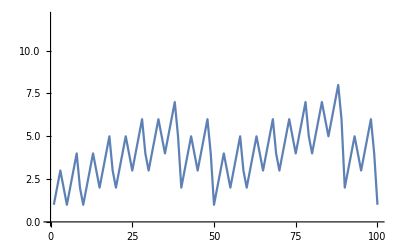
| 期望输出： |  
  | -Graphics- |

创建一个包含边框的 Range[10] 的点集图。»

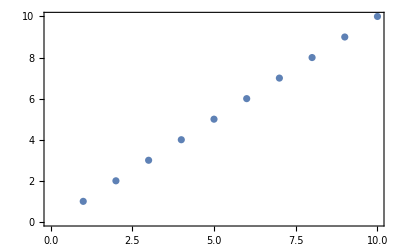
| 期望输出： |  
  | -Graphics- |

创建一个包含边框的 Range[10] 的点集图，并使用黄色背景。»

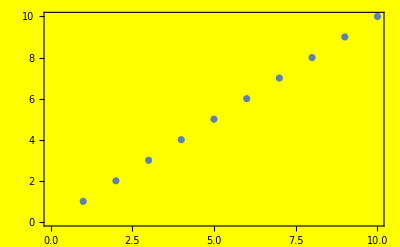
| 期望输出： |  
  | -Graphics- |

创建一个包含边框的 Range[10] 的点集图列表，其大小以 10 为步长从 50 变化到 150。»

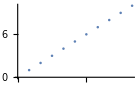
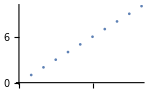
| 期望输出： |  
  | {,,,,,,,,,-Graphics-,-Graphics-} |

将前 20 个数字平方绘制为线条图，并填充到轴上。»

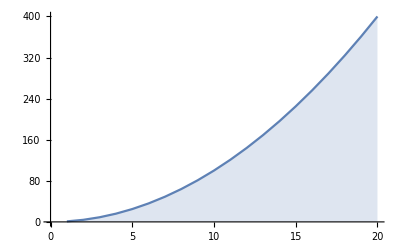
| 期望输出： |  
  | -Graphics- |

绘制珠穆朗玛峰周围地区的浮雕地图，并画一个半径为 100 英里的圆盘。»

| 期望输出： |  
  | -Graphics- |

创建一个宽高比为 1 的 Range[10]的点集图。»

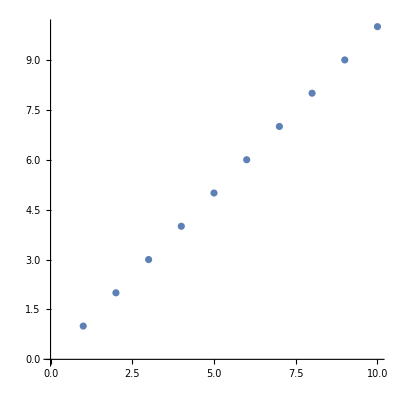
| 期望输出： |  
  | -Graphics- |

创建一个操作界面，使正六边形图像的宽高比从 0.1 到 5 之间变化。»

| 期望输出： |  
  |  |

创建一个过去一周巴黎气温的图，图的范围限制在 50 到 80 度之间。»

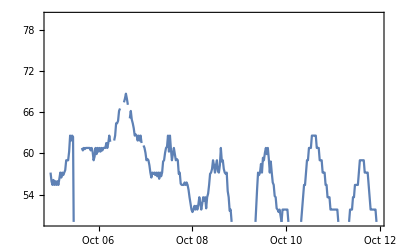
| 期望输出： |  
  | -Graphics- |

问&答

我怎样才能得到一个函数的选项列表？

查阅文档。或者使用形如 Options[WordCloud] 的方式来查询。另外，每当你开始输入一个选项的名称时，你会看到一个可能的自动完成列表。

我怎样才能找到一个选项的所有可能设置？

请查看该选项的文档。另外，当你输入 → 时，你通常会得到一个可能的常用设置的列表。

选项→值的内部是什么样的？

它是 Rule[选项,值]。在 Wolfram 语言中，很多地方都使用了规则。a→b 通常被读作“a goes to b”或“a arrow b”。

什么时候选项的值是以字符串的形式给出的？

只有一小部分标准选项设置(如 Automatic、None 和 All)不是字符串。特定选项的专门设置通常都是字符串。

能否重新设置一个选项的默认值？

是的，可以使用 SetOptions。但你必须小心，不要忘记你已经进行了修改。

技术笔记

许多选项可以被设置为纯函数(详见第 26 节)。把括号放在正确的地方很重要，如 ColorFunction→(Hue[#/4]&)，否则你不会得到正确的含义。

$FontFamilies 将给出一个 FontFamily 的可能值列表。

探索更多

Wolfram 语言中的图形选项指南 »

Wolfram 语言中的样式选项指南 »